```mathematica
proto[x_ ,μ_] :=PDF[ NormalDistribution[μ,0.1],x];
f1[x_ ]:=proto[x,1];
f2[x_ ]:=proto[x,-1];
f0[x_ ,μ_]:=proto[x,μ];
h[x_,θ_]:=f0[x ,θ]+f1[x]+f2[x];
```

```mathematica
NIntegrate[f0[x,θ]+f2[x] Log[(f0[x,θ]+f2[x])/h[x,θ]]/.θ->5,{x,-100000,100000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {387.517}. NIntegrate obtained 6.55252×10^-77 and 6.55252×10^-77 for the integral and error estimates.

6.55252×10^-77

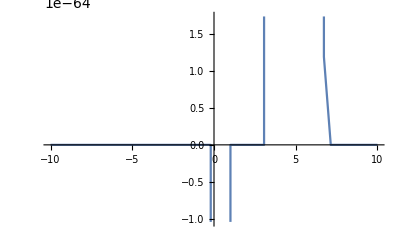

```mathematica
Plot[f0[x,θ]+f2[x] Log[(f0[x,θ]+f2[x])/h[x,θ]]/.θ->5, {x,-10,10}]
```

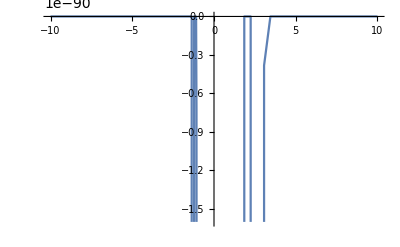

```mathematica
Plot[(f0[x,θ]+f2[x]) Log[(f0[x,θ]+f2[x])/h[x,θ]] +
(f0[x,θ]+f1[x]) Log[(f0[x,θ]+f1[x])/h[x,θ]] +
(f2[x]+f1[x] )Log[(f2[x]+f1[x])/h[x,θ]]/.θ->5, {x,-10,10}]
```

```mathematica
NIntegrate[(f0[x,θ]+f2[x]) Log[(f0[x,θ]+f2[x])/h[x,θ]] +
(f0[x,θ]+f1[x]) Log[(f0[x,θ]+f1[x])/h[x,θ]] +
(f2[x]+f1[x] )Log[(f2[x]+f1[x])/h[x,θ]]/.θ->-1, {x,-Infinity,Infinity}]
```

-1.38629

Here is an alarming result:

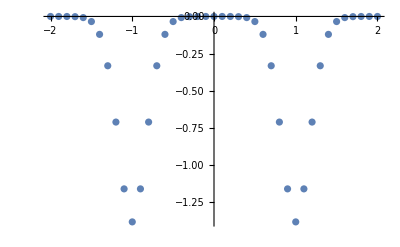

```mathematica
ListPlot[Table[{t,NIntegrate[(f0[x,θ]+f2[x]) Log[(f0[x,θ]+f2[x])/h[x,θ]] +
(f0[x,θ]+f1[x]) Log[(f0[x,θ]+f1[x])/h[x,θ]] +
(f2[x]+f1[x] )Log[(f2[x]+f1[x])/h[x,θ]]/.θ->t, {x,-Infinity,Infinity}]},{t,-2,2,0.1}]]
```

The last term seems to represent the whole answer

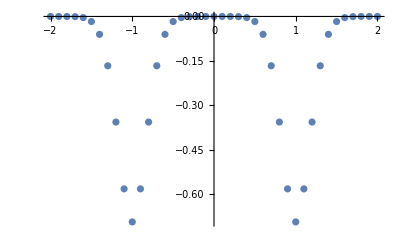

```mathematica
ListPlot[Table[{t,NIntegrate[
(f2[x]+f1[x] )Log[(f2[x]+f1[x])/h[x,θ]]/.θ->t, {x,-Infinity,Infinity}]},{t,-2,2,0.1}]]
```

Each loss function term wants f0 to be like the f that is left out in the numerator

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.969291}. NIntegrate obtained -9.71985×10^-18 and 2.1098×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.99228}. NIntegrate obtained -7.83291×10^-18 and 2.13167×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

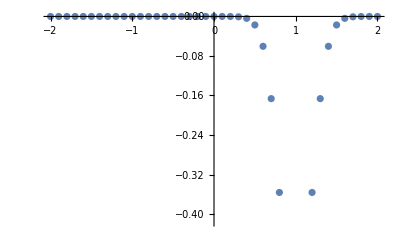

```mathematica
ListPlot[Table[{t,NIntegrate[(f0[x,θ]+f2[x]) Log[(f0[x,θ]+f2[x])/h[x,θ]] /.θ->t, {x,-Infinity,Infinity}]},{t,-2,2,0.1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.954258}. NIntegrate obtained -3.92861×10^-12 and 8.05704×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.657001}. NIntegrate obtained -1.93477×10^-15 and 5.77662×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.590101}. NIntegrate obtained -6.44821×10^-19 and 1.32497×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

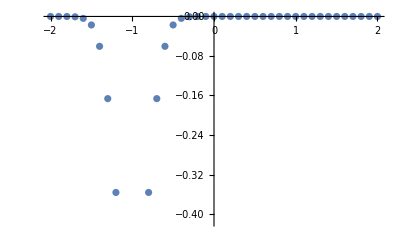

```mathematica
ListPlot[Table[{t,NIntegrate[
(f0[x,θ]+f1[x]) Log[(f0[x,θ]+f1[x])/h[x,θ]] /.θ->t, {x,-Infinity,Infinity}]},{t,-2,2,0.1}]]
```

What changes when we normalize the pdfs properly?

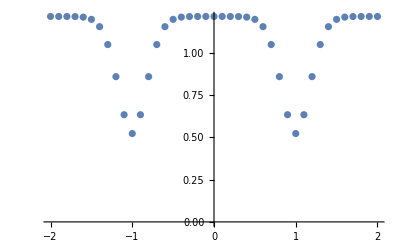

```mathematica
ListPlot[Table[{t,NIntegrate[((f0[x,θ]+f2[x])/2)  Log[((f0[x,θ]+f2[x])3)/(2 h[x,θ])] +
((f0[x,θ]+f1[x]) /2)Log[((f0[x,θ]+f1[x])3)/(2h[x,θ])] +
((f2[x]+f1[x] )/2)Log[((f2[x]+f1[x])3)/(2h[x,θ])]/.θ->t, {x,-Infinity,Infinity}]},{t,-2,2,0.1}]]
```

All the KL divergences are positive... this is comforting but actually KL diverges are only guaranteed to be positive for discrete distributions anyway.

To be honest, this is all lies anyway since we have assumed a parametric form for f0 as a gaussian...

```mathematica
f0[x_,m1_,m2_]:=PDF[ NormalDistribution[m1,0.1],x]/2 + PDF[ NormalDistribution[m2,0.1],x]/2;
h[x_,m1_,m2_]:=bimodal[x,m1,m2]+f1[x]+f2[x];
```

```mathematica
Plot3D[
NIntegrate[((f0[x,m1,m2]+f2[x])/2)  Log[((f0[x,m1,m2]+f2[x])3)/(2 h[x,m1,m2])] +
((f0[x,m1,m2]+f1[x]) /2)Log[((f0[x,m1,m2]+f1[x])3)/(2h[x,m1,m2])] +
((f2[x]+f1[x] )/2)Log[((f2[x]+f1[x])3)/(2h[x,m1,m2])], {x,-Infinity,Infinity}],
{m1,-2,2},{m2,-2,2},PlotPoints->10,Mesh->All,MaxRecursion->0]
```

-Graphics3D-

Great this is what we hoped to see, a bimodal mixture is better than unimodal

```mathematica
Plot3D[
NIntegrate[
((f2[x]+f1[x] )/2)Log[((f2[x]+f1[x])3)/(2h[x,m1,m2])], {x,-Infinity,Infinity}],
{m1,-2,2},{m2,-2,2},PlotPoints->10,Mesh->All,MaxRecursion->0]
```

-Graphics3D-

This basic shape is enforced by the last term